```mathematica
(*Single Middle*)
fileXLeg="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\13Mags_singleExtraMiddle\\Bx_LegAverage_13Mags_singleExtraMiddle.txt";
fileXTop="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\13Mags_singleExtraMiddle\\Bx_TopAverage_13Mags_singleExtraMiddle.txt";
fileYLeg="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\13Mags_singleExtraMiddle\\By_LegAverage_13Mags_singleExtraMiddle.txt";
fileYTop="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\13Mags_singleExtraMiddle\\By_TopAverage_13Mags_singleExtraMiddle.txt";
```

```mathematica
(*Two Middle*)
fileXLeg="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\14Mags_TwoAngled\\Bx_LegAverage_14Mags_TwoAngled.txt";
fileXTop="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\14Mags_TwoAngled\\Bx_TopAverage_14Mags_TwoAngled.txt";
fileYLeg="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\14Mags_TwoAngled\\By_LegAverage_14Mags_TwoAngled.txt";
fileYTop="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\14Mags_TwoAngled\\By_TopAverage_14Mags_TwoAngled.txt";
```

```mathematica
(*Three Middle*)
fileXLeg="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\15Mags_SingleMidleTwoAngled\\Bx_LegAverage_15Mags_SingleMidleTwoAngled.txt";
fileXTop="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\15Mags_SingleMidleTwoAngled\\Bx_TopAverage_15Mags_SingleMidleTwoAngled.txt";
fileYLeg="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\15Mags_SingleMidleTwoAngled\\By_LegAverage_15Mags_SingleMidleTwoAngled.txt";
fileYTop="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\15Mags_SingleMidleTwoAngled\\By_TopAverage_15Mags_SingleMidleTwoAngled.txt";
```

```mathematica
(*Star*)
fileXLeg="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\Star\\Bx_LegAverage_StarMags.txt";
fileXTop="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\Star\\Bx_TopAverage_StarMags.txt";
fileYLeg="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\Star\\By_LegAverage_StarMags.txt";
fileYTop="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana_spin\\The_Malcolm_Project\\C_Braiding\\TriJunction_Output\\Star\\By_TopAverage_StarMags.txt";
```

```mathematica
tst=Import[fileYLeg,{"Lines",1}];
```

```mathematica
MagXLeg={};
For[l=1,l≤151,l++,
out=Import[fileXLeg,{"Lines",l}];
mtp=ToExpression[out];
MagXLeg=Join[MagXLeg,{mtp}];
];
```

```mathematica
MagYLeg={};
For[l=1,l≤151,l++,
out=Import[fileYLeg,{"Lines",l}];
mtp=ToExpression[out];
MagYLeg=Join[MagYLeg,{mtp}];
];
```

```mathematica
MagXTop={};
For[l=1,l≤141,l++,
out=Import[fileXTop,{"Lines",l}];
mtp=ToExpression[out];
MagXTop=Join[MagXTop,{mtp}];
];
```

```mathematica
MagYTop={};
For[l=1,l≤141,l++,
out=Import[fileYTop,{"Lines",l}];
mtp=ToExpression[out];
MagYTop=Join[MagYTop,{mtp}];
];
```

```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=250;
NxM=40;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw;
tsw=4.0;
μ=0.0;
B=2Δ;

tϕ1=0.4ts;
tϕ2=0.4ts;
tϕ3=0.4ts;
αϕ=0.0;

ϕ=0.5 π;
ϕ3=0;


gx=0.02;
gy=0.02;


(*
(*For two middle*)
gx=0.0104;
gy=0.0104;
*)
```

```mathematica
MagΔXTop=Table[gx*MagXTop[[Ceiling[ii*Length[MagXTop]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
MagΔYTop=Table[gy*MagYTop[[Ceiling[ii*Length[MagYTop]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
GapTop=Table[Δ,{i,1,Length[MagΔXTop]}];
MagΔXLeg=Table[gx*MagXLeg[[Ceiling[ii*Length[MagXLeg]/(Nx)]]],{ii,1,Nx}];
MagΔYLeg=Table[gx*MagYLeg[[Ceiling[ii*Length[MagYLeg]/(Nx)]]],{ii,1,Nx}];
GapLeg=Table[Δ,{i,1,Length[MagΔXLeg]}];
```

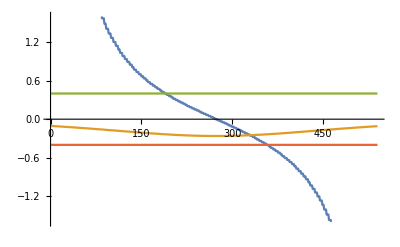

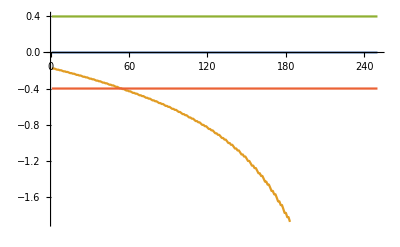

```mathematica
ListPlot[{MagΔXTop,MagΔYTop,GapTop,-GapTop},Joined->True]
ListPlot[{MagΔXLeg,MagΔYLeg,GapLeg,-GapLeg},Joined->True]
```

```mathematica
MagX1=Table[MagΔXTop[[i]],{i,1,Nx}];
MagY1=Table[MagΔYTop[[i]],{i,1,Nx}];
MagXM=Table[MagΔXTop[[i]],{i,Nx+1,Nx+NxM}];
MagYM=Table[MagΔYTop[[i]],{i,Nx+1,Nx+NxM}];
MagX2=Table[MagΔXTop[[i]],{i,Nx+NxM+1,2Nx+NxM}];
MagY2=Table[MagΔYTop[[i]],{i,Nx+NxM+1,2Nx+NxM}];
MagX3=MagΔXLeg;
MagY3=MagΔYLeg;
```

```mathematica
H[θM_]:=Block[{Hsp},
ϵ0=2ts Cos[Pi/(Nx+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+MagY1,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-MagY1,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->MagX1,Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->MagX1,Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+MagYM,Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-MagYM,Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->MagXM,Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->MagXM,Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+MagY2,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-MagY2,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->MagX2,Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->MagX2,Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Third Chain*)
H3σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+MagY3,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-MagY3,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ12τ11=SparseArray[{Band[{1,1}]->ⅈ MagX3,Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];
H3σ21τ11=SparseArray[{Band[{1,1}]->-ⅈ MagX3,Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];

H3σ12τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];
H3σ21τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];

H3τ11=SparseArray[ArrayFlatten[{{H3σ11τ11,H3σ12τ11},{H3σ21τ11,H3σ22τ11}}]];
H3τ22=-H3τ11;
H3τ12=SparseArray[ArrayFlatten[{{0,H3σ12τ12},{H3σ21τ12,0}}]];
H3τ21=Conjugate[Transpose[H3τ12]];

H33=SparseArray[ArrayFlatten[{{H3τ11,H3τ12},{H3τ21,H3τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

HM3=SparseArray[{{NxM/2,1}->tϕ3,{NxM+NxM/2,Nx+1}->tϕ3,{2NxM+NxM/2,2Nx+1}->-tϕ3,{3NxM+NxM/2,3Nx+1}->-tϕ3},{4NxM,4Nx}];
H3M=Conjugate[Transpose[HM3]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0,0},{HM1,HMM,HM2,HM3},{0,H2M,H22,0},{0,H3M,0,H33}}]];

Hsp
];
```

```mathematica
{e,ψ}=Transpose[Sort[Transpose[Eigensystem[H[0.],-20]]]];
```

```mathematica
n=11;
e[[n]]/Δ
ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,1,Nx}];
ψAMue=Table[{i-1-3Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,4Nx,4Nx+NxM}];
ψA2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψA3ue=Table[{i+1-4Nx-4NxM-4Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx}];
ψbar=Join[ψA1ue,ψAMue,ψA2ue];
ψleg=ψA3ue;
```

3.10415×10^-7

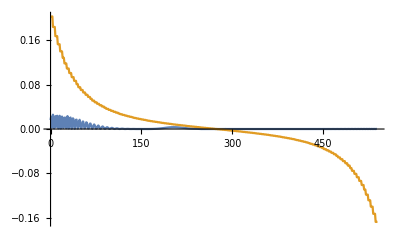

```mathematica
w=Max[Table[ψbar[[i,2]],{i,1,Length[ψbar]}]];
ListPlot[{ψbar,w MagΔXTop},Joined->True,PlotRange->All]
```

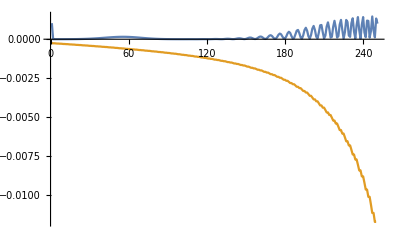

```mathematica
w=Max[Table[ψleg[[i,2]],{i,1,Length[ψleg]}]];
ListPlot[{ψleg,w MagΔYLeg},Joined->True,PlotRange->All]
```